```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/zack/Documents/ignition/cantera/ratematrix

```mathematica
(* Benchmark scipy's eigenvalues and mathematica's. Sort the eigenvalues and eigenvectors in python before outputting..*)
```

```mathematica
filebase="data/h2o2test"
dat=Import[filebase<>"out.dat"];
{temp,press, atoms, dim,runtime} = dat[[-2,1;;5]]
elements=dat[[-1]];
file=OpenRead[filebase<>"ratematrix.npy","BinaryFormat"->True];
A=Transpose[Partition[BinaryReadList[file,"Real64"][[17;;-1]],dim]];
Close[file];
file=OpenRead[filebase<>"eigenvalues.npy","BinaryFormat"->True];
evals=BinaryReadList[file,"Real64"][[17;;-1]];
Close[file];
file=OpenRead[filebase<>"eigenvectors.npy","BinaryFormat"->True];
evecs=Partition[BinaryReadList[file,"Real64"][[17;;-1]],dim];
Close[file];
file=OpenRead[filebase<>"spatoms.npy","BinaryFormat"->True];
spatoms=Partition[BinaryReadList[file,"Integer64"][[17;;-1]],Length[elements]];
Close[file];
file=OpenRead[filebase<>"multiindices.npy","BinaryFormat"->True];
multiindices=Partition[BinaryReadList[file,"Integer64"][[17;;-1]],Length[spatoms]];
Close[file];
spforms=Table[DisplayForm[RowBox[Table[If[spatoms[[i,j]]>0,Subscript[elements[[j]],spatoms[[i,j]]],""],{j,1,Length[elements]}]]],{i,1,Length[spatoms]}];
multiforms=Table[Total[multiindices[[i]]*spforms],{i,1,dim}];
p=Grid[{{MatrixPlot[A,ImageSize->300,FrameTicks->{Table[Round[i],{i,1,dim,(dim-1)/5}],Table[Round[i],{i,1,dim,(dim-1)/5}]},FrameLabel->{{i,"Rate matrix"},{j,None}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{65,10},{65,65}}],ListPlot[Sort[Log[-evals]],PlotRange->All,AspectRatio->1,Axes->False,Frame->True,ImageSize->300,FrameTicks->{{Automatic,None},{Table[Round[i],{i,1,dim,(dim-1)/5}],None}},FrameLabel->{{Log[-Subscript[λ,i]],None},{i,Eigenvalues}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{65,10},{65,65}}]},{MatrixPlot[Reverse[Eigensystem[A][[2]]],ImageSize->300,FrameTicks->{Table[Round[i],{i,1,dim,(dim-1)/5}],Table[Round[i],{i,1,dim,(dim-1)/5}]},FrameLabel->{{i,"Left eigenvectors"},{j,None}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{65,10},{65,65}}],ListPlot[Abs[Eigensystem[A][[2,-1]]],ImageSize->300,PlotRange->All,Axes->False,Frame->True,FrameLabel->{{Subscript[P,i],None},{i,"Steady distribution"}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[Round[i],{i,1,dim,(dim-1)/5}],None}},PlotStyle->Directive[PointSize[0.05]],ImagePadding->{{65,10},{65,65}}]}}]
Export["plots/example.pdf",p]
multiforms[[Reverse[Ordering[Abs[Eigensystem[A][[2,-1]]]]]]]
```

data/h2o2test

{1500,1,26,943,4.51156}

-Graphics-

plots/example.pdf

{5 (Ar_1)+7 (O_1 H_2),5 (Ar_1)+H_2+5 (O_1 H_2)+O_2 H_2,5 (Ar_1)+2 (H_2)+5 (O_1 H_2)+O_2,5 (Ar_1)+4 (H_2)+3 (O_1 H_2)+2 (O_2),5 (Ar_1)+H_1+O_1 H_1+6 (O_1 H_2),934,5 (Ar_1)+9 (H_1)+2 (O_1)+O_1 H_1+2 (O_2 H_2),5 (Ar_1)+8 (H_1)+H_2+3 (O_1)+2 (O_2 H_2),5 (Ar_1)+10 (H_1)+3 (O_1)+2 (O_2 H_2),5 (Ar_1)+6 (H_1)+H_2+O_1+3 (O_2 H_2)}
 |  |  |  |

## Runtimes

{{9,19,0.0115093,332,9},{12,48,0.0813439,1225,12},{15,89,0.596218,3588,15},{18,177,4.28785,9583,18},{21,298,24.6733,22616,21},{24,516,133.293,50049,24},{27,807,644.169,102480,27}}

{{36,2803,3.06788,661388,36},{9,19,0.00170795,332,9},{12,48,0.00387898,1225,12},{15,89,0.0102981,3588,15},{18,177,0.0286813,9583,18},{21,298,0.0732696,22616,21},{24,516,0.173361,50049,24},{27,807,0.389899,102480,27},{30,1277,0.80559,200145,30},{33,1888,1.5921,370476,33},{36,2803,3.16585,661388,36}}

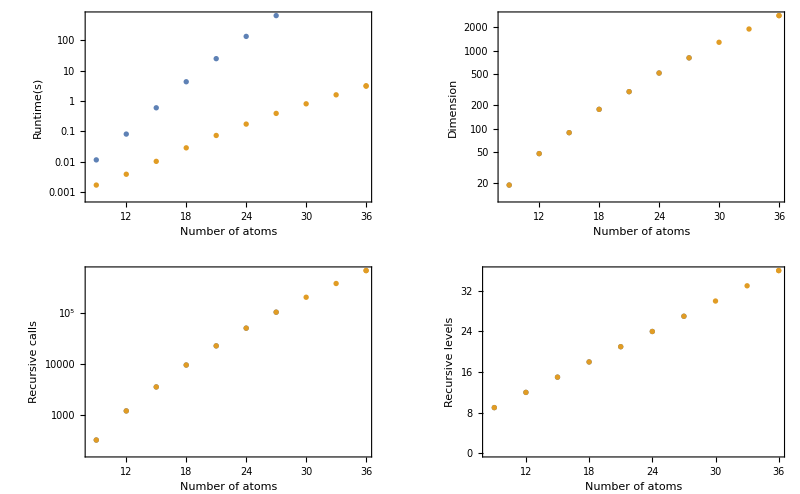

plots/runtimes.pdf

```mathematica
dat=Import["data/runtimesout.dat"]
dat2=Import["data/runtimes2out.dat"]
p=GraphicsGrid[{{ListLogPlot[{{#[[1]],#[[2]]}&/@dat[[All,{1,3}]],{#[[1]],#[[2]]}&/@dat2[[All,{1,3}]]},ImageSize->300,Frame->True,Axes->False,FrameLabel->{"Number of atoms","Runtime(s)"}, FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[16,Black]],ListLogPlot[{{#[[1]],#[[2]]}&/@dat[[All,{1,2}]],{#[[1]],#[[2]]}&/@dat2[[All,{1,2}]]},ImageSize->300,Frame->True,Axes->False,FrameLabel->{"Number of atoms","Dimension"}, FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[16,Black]]},{ListLogPlot[{{#[[1]],#[[2]]}&/@dat[[All,{1,4}]],{#[[1]],#[[2]]}&/@dat2[[All,{1,4}]]},ImageSize->300,Frame->True,Axes->False,FrameLabel->{"Number of atoms","Recursive calls"}, FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[16,Black]],ListPlot[{{#[[1]],#[[2]]}&/@dat[[All,{1,5}]],{#[[1]],#[[2]]}&/@dat2[[All,{1,5}]]},ImageSize->300,Frame->True,Axes->False,FrameLabel->{"Number of atoms","Recursive levels"}, FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[16,Black]]}}]
Export["plots/runtimes.pdf",p]
```

## Temperature - pressure sweep

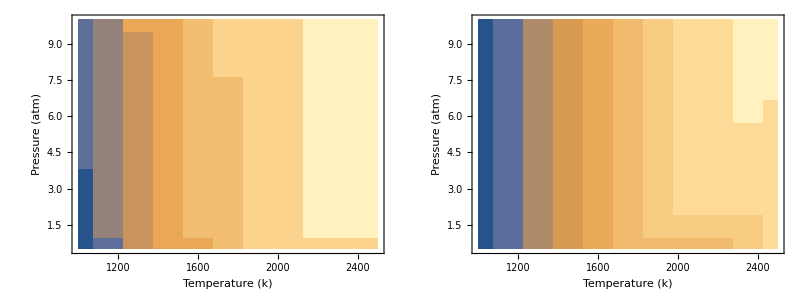

plots/sweep.pdf

```mathematica
sweep=Import["data/sweepout.dat"];
p=Grid[{{ListContourPlot[{#[[1]],#[[2]],Log[-#[[-2]]]}&/@sweep,ImageSize->350,LabelStyle->Directive[16,Black],FrameLabel->{{"Pressure (atm)",None},{"Temperature (k)",Log[-Subscript[λ,1]]}},FrameStyle->Directive[Black,AbsoluteThickness[2]],InterpolationOrder->0],ListContourPlot[{#[[1]],#[[2]],Log[-#[[-3]]]}&/@sweep,ImageSize->350,LabelStyle->Directive[16,Black],FrameLabel->{{"Pressure (atm)",None},{"Temperature (k)",Log[-Subscript[λ,2]]}},FrameStyle->Directive[Black,AbsoluteThickness[2]],InterpolationOrder->0]}}]
Export["plots/sweep.pdf",p]
```

## Temperature - atoms sweep

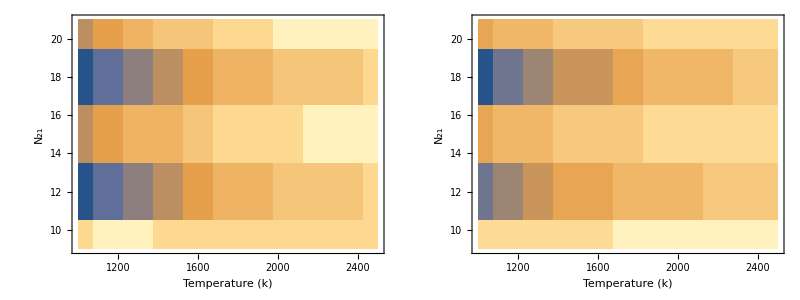

plots/sweep2.pdf

```mathematica
sweep2=Import["data/sweep2out.dat"];
p=Grid[{{ListContourPlot[{#[[1]],#[[3]],Log[-#[[-2]]]}&/@sweep2,ImageSize->350,LabelStyle->Directive[16,Black],FrameLabel->{{Subscript[N,atoms],None},{"Temperature (k)",Log[-Subscript[λ,1]]}},FrameStyle->Directive[Black,AbsoluteThickness[2]],InterpolationOrder->0,PlotRange->All],ListContourPlot[{#[[1]],#[[3]],Log[-#[[-3]]]}&/@sweep2,ImageSize->350,LabelStyle->Directive[16,Black],FrameLabel->{{Subscript[N,atoms],None},{"Temperature (k)",Log[-Subscript[λ,2]]}},FrameStyle->Directive[Black,AbsoluteThickness[2]],InterpolationOrder->0,PlotRange->All]}}]
Export["plots/sweep2.pdf",p]
```